```mathematica
optimaldistance1Dmodel[ballspeed,defenderspeed]:=Module[{vars},body]
```

```mathematica
passgraphPlot1D[modelspecifcation]
```

```mathematica
{courtX,courtY}={52,94};
```

```mathematica
court=Rectangle[{0,0},{courtX,courtY}]
```

Rectangle[{0,0},{52,94}]

```mathematica
defenderpositions=RandomPoint[court,5]
```

{{36.6368,61.0159},{19.2243,78.5039},{28.1256,90.0503},{45.9255,18.5199},{24.3791,68.2941}}

```mathematica
defenderZOC=Disk[#,3]&/@defenderpositions
```

{Disk[{36.6368,61.0159},3],Disk[{19.2243,78.5039},3],Disk[{28.1256,90.0503},3],Disk[{45.9255,18.5199},3],Disk[{24.3791,68.2941},3]}

```mathematica
passerZOC=Disk[RegionCentroid@court]
```

Disk[{26,47}]

```mathematica
defenderZOC2=Table[Disk[dp,EuclideanDistance[dp,RegionCentroid@court]/4],{dp,defenderpositions}]
```

{Disk[{36.6368,61.0159},4.39877],Disk[{19.2243,78.5039},8.05607],Disk[{28.1256,90.0503},10.7757],Disk[{45.9255,18.5199},8.68958],Disk[{24.3791,68.2941},5.33893]}

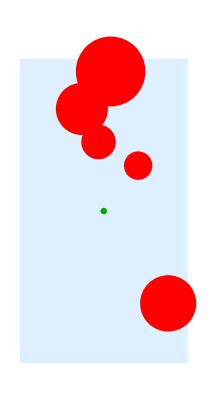

```mathematica
Graphics[{LightBlue,court,Red,defenderZOC2,Darker@Green,passerZOC}]
```

```mathematica
visfunction[dps_List]:=Manipulate[
Module[{halfcourt,passerposition,defenderpositions,defenderZOC,passerZOC,ballspeed},
ballspeed=passvelocity;
passerposition={26,0};
halfcourt=Rectangle[{0,0},{52,47}];
passerZOC=Disk[passerposition,1];
defenderpositions=dps;
defenderZOC=Map[Disk[#,EuclideanDistance[#,passerposition]/ballspeed]&,defenderpositions];
Graphics[{LightBlue,halfcourt,LightRed,defenderZOC,Darker@Green,passerZOC}]
],{{passvelocity,10},1,10},ControlPlacement->Top,SaveDefinitions->True,TrackedSymbols:>passvelocity]
```

```mathematica
RandomPoint[RegionBoundary@Disk[{52/2,0},15,{0,Pi}],5]
```

{{40.6187,0.},{36.1309,11.0618},{11.4764,3.75042},{28.6383,0.},{29.555,14.5726}}

```mathematica
visfunction[{{40.61870934998925,0.},{36.13092463559059,11.061842795302406},{11.476421012172667,3.750420427677459},{28.638279685836054,0.},{29.555029139903517,14.57263764095014}}]
```

```mathematica
Manipulate[
Module[{halfcourt,passerposition,defenderpositions,defenderZOC,passerZOC,ballspeed},
ballspeed=passvelocity;
passerposition={26,0};
halfcourt=Rectangle[{0,0},{52,47}];
passerZOC=Disk[passerposition,1];
SeedRandom[1234];
defenderpositions=RandomPoint[halfcourt,5];
defenderZOC=Map[Disk[#,EuclideanDistance[#,passerposition]/ballspeed]&,defenderpositions];
Graphics[{LightBlue,halfcourt,LightRed,defenderZOC,Darker@Green,passerZOC}]
],{{passvelocity,10},1,10},ControlPlacement->Top,SaveDefinitions->True,TrackedSymbols:>passvelocity]
```

```mathematica
?Interval
```

```mathematica
?RandomReal
```

```mathematica
?Rectangle
```